```mathematica
format[num_]:=ToString@NumberForm[num,{3,0},NumberPadding->{"0", ""},NumberSigns->{"", ""}];
f[num_]:=Module[{},
json=Import[NotebookDirectory[]<>"sample/"<>format[num]<>".json"];
nns=json[[1]]//Length;
notes=Table[{"note","duration"}/.json[[1]][[i]],{i,1,nns}];
durationsSorted=Sort[Function[x,Round[x[[2]]/40]]/@notes];
durations=Function[x,Min[32,Round[x[[2]]/40]]]/@notes;
features=Function[x,Min[32,Round[x[[2]]/40]]*128+x[[1]]]/@notes;
notes2=Function[x,x[[1]]+1]/@notes;(* add 1 => (1,128) *)
times=Table[Total[durations[[1;;i]]],{i,1,nns}];
notes2
]
```

```mathematica
(*data=TemporalData[{notes2},{times}]*)
data=Table[f[i],{i,1,909}];
ls=Length/@data;
data=TemporalData[data,{0}]
```

TemporalData[…]

```mathematica
Function[x,Module[{},
Echo[x];
P1=EstimatedProcess[data,
HiddenMarkovProcess[x,128],
WorkingPrecision->MachinePrecision
];
Mean[LogLikelihood[P1, #]&/@data["Paths"]]
]
]/@{16,32,64,128,256,512}
```

16

32

64

128

256

512

{-1415.27,-1415.27,-1415.27,-1415.27,-1415.27,-1415.27}

TemporalData[…]

-293.005

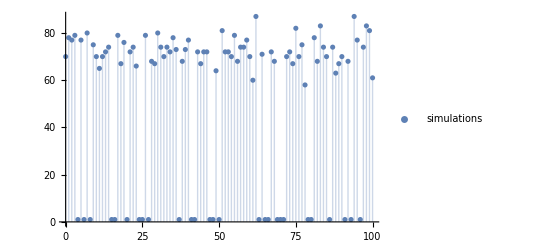

```mathematica
l=100;
simss=Table[RandomFunction[P1,{0,l}],{i,3}];
sims=simss[[1]]
LogLikelihood[P1,sims]
ListPlot[sims["Paths"],PlotStyle->{Thick,Dashed},PlotLegends->{"simulations"},Filling->Axis]
```

```mathematica
GenChord[x_]:=If[RandomReal[1]>0.5,{x,x+4,x+7},{x,x+3,x+7}]
```

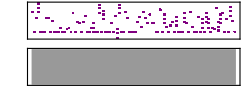

/mnt/onedrive/onedrive/OldStuff/Research/MM/mcmusic/mma001.mid

```mathematica
unit=0.24;
shifts={0,-16,-9};
sound=Sound[
Table[
Sound[
If[#[[2]]!=1,
SoundNote[If[RandomReal[1]>0.8,GenChord[#[[2]]-64+shifts[[i]]],#[[2]]-64+shifts[[i]]],unit,"Piano"],
SoundNote["C",unit,"Piano",SoundVolume->0]
]&/@simss[[i]]["Paths"][[1]],{0,unit*l}
],
{i,1,1}
]
]
(*EmitSound@sound*)
Export[NotebookDirectory[]<>"mma001.mid",sound]
```

```mathematica
P1[[3]]//Dimensions
{pi,m,em}={P1[[1]],P1[[2]],P1[[3]]};
```

{256,128}